{{a→27.56,b→-0.0574286,c→0.000285714}}

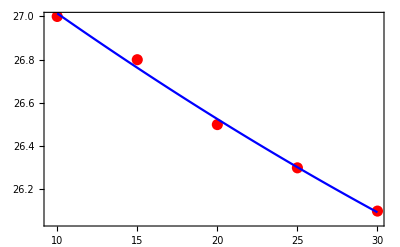

```mathematica
Tx={10.0, 15.0, 20.0, 25.0, 30.0};
Ty={27.0,26.8,26.5,26.3,26.1};
xy=Table[{Tx[[i]],Ty[[i]]},{i,1,5}];
q[a_,b_,c_]:=Sum[(a+b Tx[[i]]+ c Tx[[i]]^2-Ty[[i]])^2,{i,1,5}];
Ans=NSolve[{D[q[a,b,c],a]==0,D[q[a,b,c],b]==0,D[q[a,b,c],c]==0}, {a,b,c},Reals]
P1=ListPlot[xy, PlotRange->All, PlotTheme->"Scientific", PlotStyle->{Red,PointSize[0.02]}];
f[x_]:=Limit[a,Ans[[1]][[1]]]+Limit[b,Ans[[1]][[2]]]x+Limit[c,Ans[[1]][[3]]] x^2;
P2=Plot[f[x],{x,10,30},PlotTheme->"Scientific", PlotStyle->{Blue}];
Show[P1,P2]
```